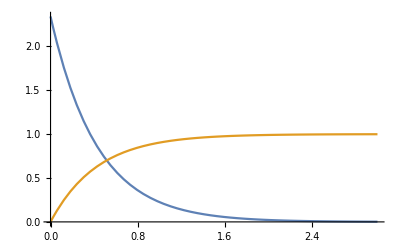

```mathematica
w = 8.96*10^(-3)*2.613*10^(2);
Plot[{w*Exp[-x*w],1-Exp[-x*w]},{x,0,3}, PlotRange->{0,w}]
```

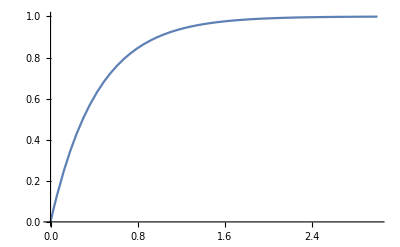

```mathematica
Plot[1-Exp[-x*w],{x,0,3},PlotRange->{0,1}]
```

```mathematica
w1 = 1; 
w2 = 2; 
x1 = 1.5;
```

```mathematica
A = 1/(1/w1 - Exp[-w1*x1]/w1 + Exp[-w1*x1]/w2);
B = A*Exp[-w1*x1];
```

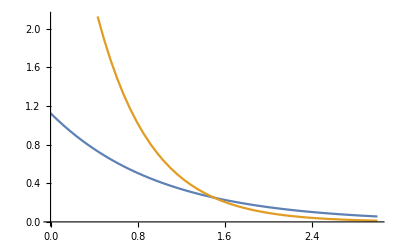

```mathematica
Plot[{A*Exp[-w1*x],B*Exp[-w2(x-x1)]},{x,0,3}]
```

```mathematica
Integrate[A*Exp[-w1*x],{x,0,x1}]
```

0.874425

```mathematica
Integrate[B*Exp[-w2*(x-x1)],{x,x1,10000}]
```

0.125575

```mathematica
0.87442515194750050+0.12557484805249935
```

1.